{957→957/1000,741→741/1000,883→883/1000,655→131/200,456→57/125,711→711/1000,510→51/100,843→843/1000,656→82/125,327→327/1000}

{141→141/1000,600→3/5,99→99/1000,977→977/1000,210→21/100,980→49/50,770→77/100,850→17/20,788→197/250,339→339/1000}

197/200

General::munfl: 0.0000204286^133.985 is too small to represent as a normalized machine number; precision may be lost.

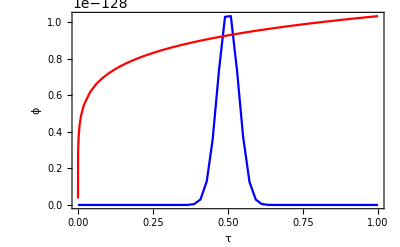

```mathematica
(*Constants*)
n=1000;
observe=0.1;
k=10;
SeedRandom[123];

(*Set the scaling factor as desired*)
scale=1; 

(*Generate w as a vector according to the inc_weights function*)
w=Array[#^scale/n&,n];


(*Calculate the number of observations to sample*)
numObservations=Round[n*observe];

(*Perform weighted sampling without replacement*)
Obs=RandomSample[w->Thread[Range[n]->w],numObservations];

(*Full list of pairs*)
fullPairs=Thread[Range[n]->w];
(*Remaining pairs after excluding Obs*)

Mis=Complement[fullPairs,Obs];

delta=Total[Mis[[All,2]]];

(*Define z(h) function*)
z[h_]:=delta-1/h-Sum[w[[i]]/(2^(h*w[[i]])-1),{i,Obs[[All,1]]}];

(*Find h using FindRoot with the Newton-Raphson method,starting with an initial guess*)
hSolution=FindRoot[z[h]==0,{h,1/delta},Method->"Newton"];

(*Extract the value of h from the solution*)
h=h/. hSolution;

(*Define Phi function*)
Phi[tau_]:=h*delta*tau^(h*delta-1)*Product[(1-tau^(h*w[[i]])),{i,Obs[[All,1]]}];



(*Randomly select k threads from Obs and Mis each*)
selectedObs=RandomSample[Obs,k];
selectedMis=RandomSample[Mis,k];
selectedObs
selectedMis
di = Total[selectedObs[[All,2]]]-Total[selectedMis[[All,2]]]


eta[tau_] := tau^(h*di)*(delta+di)/delta*Product[(1-tau^(h*w[[i]])),{i,selectedMis[[All,1]]}]/Product[(1-tau^(h*w[[i]])),{i,selectedObs[[All,1]]}]


(*Plot Phi function with its own scale on the left*)
phiPlot=Plot[Phi[tau],{tau,0,1},PlotStyle->Blue,AxesLabel->{"τ",None},PlotRange->All];

(*Plot eta function with its own scale,invisible for now to determine range*)
etaPlot=Plot[eta[tau],{tau,0,1},PlotStyle->Red,PlotRange->All];

(*Extract plot ranges to find scaling factor*)
phiPlotRange=AbsoluteOptions[phiPlot,PlotRange][[1,2,2]];
etaPlotRange=AbsoluteOptions[etaPlot,PlotRange][[1,2,2]];

(*Scale factor to match eta's range to phi's for visual consistency*)
scaleFactor=phiPlotRange[[2]]/etaPlotRange[[2]];

(*Manually create ticks for the right y-axis corresponding to eta's values*)
rightAxisTicks=Table[{i,NumberForm[i/scaleFactor,{5,2}]},{i,0,phiPlotRange[[2]],phiPlotRange[[2]]/10}];

(*Plot eta adjusted for combined plot,without affecting its scale for ticks*)
etaPlotAdjusted=Plot[eta[tau]*scaleFactor,{tau,0,1},PlotStyle->Red,PlotRange->All];

(*Combine the plots with manual right-axis ticks*)
Show[phiPlot,etaPlotAdjusted,PlotRange->All,Frame->True,FrameStyle->{Automatic,Blue,Automatic,Red},FrameTicks->{{Automatic,rightAxisTicks},{Automatic,None}},FrameLabel->{"τ","ϕ",None,"η"}]
```